# Deuteron content of the final 3-body state 15/08/24

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

```mathematica
dbg=False;
Hat[x_]:=√(2 x +1);
Clear[nineJSymbol]
	nineJSymbol[{j1_,j2_,j3_},{j4_,j5_,j6_},{j7_,j8_,j9_}] := Module[{kmin,kmax},
		kmin = Max[{Abs[j1-j9],Abs[j4-j8],Abs[j2-j6]}];
			kmax = Min[{Abs[j1+j9],Abs[j4+j8],Abs[j2+j6]}];
		Sum[(-1)^(2 k) (2 k+1) SixJSymbol[{j1,j4,j7},{j8,j9,k}]  SixJSymbol[{j2,j5,j8},{j4,k,j6}] SixJSymbol[{j3,j6,j9},{k,j1,j2}],{k,kmin,kmax}]]
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transform

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];

trafoToIHeNorm[normMat_]:=Block[{dbg=True},
{evaln,evecn}=Eigensystem[normMat];

diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
trafoToIHeNormStab[normMat_,cutoff_:0.0]:=Block[{dbg=True},
{evaln,evecn}=Transpose[Select[Sort[Transpose[Eigensystem[normMat]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5}; (*Spin of Excited states*)
J0=0.5; (*Spin of Ground states which consists of two channels s and d*)
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
EVthreshold=(10.)^(-8);
dH=1; (* this takes only every dH basis vector into account; ECCE: not benchmarked *)
```

```mathematica
ImgSize=900;
mnucl=938.3;
hbarc=197.3269804; (*codata*)

hbarsqO2m=hbarc^2/(2 mnucl);
(*αfine=1./137.*)
αfine=UnitConvert[Quantity[1,"FineStructureConstant"]];
hat[l_]:=Sqrt[2 l+1];

resultsDir2="/home/kirscher/kette_repo/IRS/Projection";
resultsDir="/home/kirscher/kette_repo/IRS/Projection/3body";

files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]]/Length[Subscript[I, n]];

SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

Read FORTRAN results from 
/home/kirscher/kette_repo/IRS/Projection/3body
in
float64=Real64
format for
N_bases=2
evolved bases for the expansion of the final state.

### Read H_αβ^J:=⟨α|(Ĥ)_(V18+UIX)|β⟩ and 𝕟_αβ^J:=⟨α|OverHat[𝟙]|β⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(0)^- or J^π=(1)^- or J^π=(2)^- for the negative-parity rank-1 E_1 operator perturbing a Helion;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSNormHamMat=Table[readREAL8list[#]&/@Sort[matnamesJ[[Inn]],ToExpression[StringSplit[#1,"-"][[-1]]]<ToExpression[StringSplit[#2,"-"][[-1]]]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@FSNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["Final-state-basis Dimension = ",FSbasisDim];
FSNormBare=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[1;;FSbasisDim[[Inn]][[#]]^2]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
FSHamBare=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[FSbasisDim[[Inn]][[#]]^2+1;;]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
```

Final-state-basis Dimension = {{324,324}}

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafosαβ=Table[trafoToIHeNormStab[FSNormBare[[Inn]][[#]],EVthreshold]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
fulltrafosαβInstab=Table[trafoToIHeNorm[FSNormBare[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
Print["threshold-less reordering and diagonal-normalizing basis trafo: ",Dimensions[fulltrafosαβInstab[[1]][[1]]]];
Print[EVthreshold," threshold for norm eigenvalues: ",Dimensions[fulltrafosαβ[[1]][[1]]]];
Table[Select[ArrayRules[SparseArray[Chop[Transpose[fulltrafosαβ[[nj]][[nb]]].FSNormBare[[nj]][[nb]].fulltrafosαβ[[nj]][[nb]]]]],#[[1]][[1]]!=#[[1]][[2]]&],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
FSHam=Table[Transpose[fulltrafosαβ[[nj]][[nb]]].FSHamBare[[nj]][[nb]].fulltrafosαβ[[nj]][[nb]],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
FSNorm=Table[Transpose[fulltrafosαβ[[nj]][[nb]]].FSNormBare[[nj]][[nb]].fulltrafosαβ[[nj]][[nb]],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
FSHamInstab=Table[Transpose[fulltrafosαβInstab[[nj]][[nb]]].FSHamBare[[nj]][[nb]].fulltrafosαβInstab[[nj]][[nb]],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
FSNormInstab=Table[Transpose[fulltrafosαβInstab[[nj]][[nb]]].FSNormBare[[nj]][[nb]].fulltrafosαβInstab[[nj]][[nb]],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
Print["bare/stabilized final-state dimension: ",Dimensions[FSHamBare[[1]][[1]]],"/",Dimensions[FSHam[[1]][[1]]]];
FSNormBare[[1]][[1]][[;;5,;;5]]//MatrixForm
FSNormInstab[[1]][[1]][[;;5,;;5]]//MatrixForm
FSNorm[[1]][[1]][[;;5,;;5]]//MatrixForm
```

threshold-less reordering and diagonal-normalizing basis trafo: {324,324}

1.×10^-8 threshold for norm eigenvalues: {324,324}

bare/stabilized final-state dimension: {324,324}/{324,324}

(1. | 0.179407 | 0.00391825 | 0.00115085 | 0.000410494
0.179407 | 1. | 0.0944365 | 0.0293874 | 0.0106912
0.00391825 | 0.0944365 | 1. | 0.747503 | 0.403184
0.00115085 | 0.0293874 | 0.747503 | 1. | 0.812705
0.000410494 | 0.0106912 | 0.403184 | 0.812705 | 1.)

(1. | 2.44258×10^-33 | -7.70372×10^-33 | -2.22045×10^-16 | 1.31926×10^-32
1.10818×10^-32 | 1. | 9.27847×10^-33 | 1.06195×10^-33 | -1.29975×10^-34
-5.3926×10^-33 | 8.76211×10^-34 | 1. | 4.81482×10^-33 | -4.85723×10^-17
1.66533×10^-16 | -9.25324×10^-33 | -1.54074×10^-33 | 1. | 8.47409×10^-33
1.25908×10^-32 | 1.92895×10^-33 | 2.94903×10^-17 | 1.12667×10^-32 | 1.)

(1. | -9.60978×10^-10 | 1.44096×10^-10 | 2.25519×10^-11 | -1.73228×10^-10
-7.88302×10^-10 | 1. | -1.03583×10^-9 | 1.69215×10^-10 | -2.005×10^-10
3.78359×10^-9 | -8.41922×10^-10 | 1. | -1.32353×10^-10 | 1.61962×10^-11
-6.52981×10^-10 | -1.67736×10^-10 | -4.52161×10^-10 | 1. | 2.34977×10^-10
-3.20448×10^-10 | 7.65714×10^-11 | 1.64635×10^-10 | -4.88039×10^-10 | 1.)

#### The final states

for the projection calculation, I initially chose no stabilizing elimination of small norm ev and no reordering of the basis

```mathematica
esysFSp=Table[Sort[Transpose[Eigensystem[{FSHamBare[[Inn]][[Nbb]],FSNormBare[[Inn]][[Nbb]]}]],Re[#1[[1]]]<Re[#2[[1]]]&],{Inn,Range[1,Length[Subscript[I, n]]]},{Nbb,Range[anzBas]}];
esysFSp[[1]][[1]][[1;;5,1]]
Norm[esysFSp[[1]][[1]][[1,2]]];
FSDimp=Table[Length[esysFSp[[Inn]][[Nbb]][[1]][[2]]],{Inn,Range[1,Length[Subscript[I, n]]]},{Nbb,Range[anzBas]}]
```

{-2.10137,-2.01814,-1.74578,-1.7043,-0.410946}

{{324,324}}

#### Deuteron-state expansion in the reduced final-state space

ECCE:
(0) no stabilizing transformation is employed; cf. 3-body states.
(1) post-python calculation of the Da state:
/home/kirscher/kette_repo/IRS/Projection/Sfrags_LIT_0.5^-_BasNR-1.dat   >  INLUCN  (def. nbr. of S- and D-blocks)
/home/kirscher/kette_repo/IRS/Projection/Sintw3heLIT_0.5^-_BasNR-1.dat   >  INQUA_M  (select rows which correspond to l12=0,2 and assign them to the respective 2-body block)
run src_fortran/DR2END_NORMAL.exe  ⇒  MATOUTB

```mathematica
DNormHamMat=readREAL8list[resultsDir2<>"/2body/MATOUTB"];
tmp=DNormHamMat[[Range[1,Length[DNormHamMat],2]]];

DBasisDimBare=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
Print["deuteron-basis Dimension = ",DBasisDimBare];

DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDimBare^2]],{DBasisDimBare,DBasisDimBare}][[;;;;dH,;;;;dH]];
DHam=ArrayReshape[DNormHamMat[[DBasisDimBare^2+1;;]],{DBasisDimBare,DBasisDimBare}][[;;;;dH,;;;;dH]];
```

deuteron-basis Dimension = 30

```mathematica
orderedEVDp=Sort[Transpose[Eigensystem[{DHam,DNorm}]],Re[#1[[1]]]<Re[#2[[1]]]&];
DevalGSp=orderedEVDp[[1]][[1]];
DevecGSp=orderedEVDp[[1]][[2]];
Print["Vector norm of GS (generalized EVP) = ",Norm[DevecGSp]];
Print["B(initial) = ",Style[DevalGSp,Red]," MeV"];
orderedEVDp[[1;;4,1]]
coefflisttmp=orderedEVDp[[1,2]]
Map[SetAccuracy[#,12]&,coefflisttmp]
Export["tmp.cf",Map[SetAccuracy[#,16]&,coefflisttmp],"Table"]

DBasisDim=Length[DevecGSp];
Print["Deuteron-basis Dimension = ",DBasisDim];
```

Vector norm of GS (generalized EVP) = 1.

B(initial) = -2.2124 MeV

{-2.2124,0.0149575,0.0938654,0.100022}

{-0.00347769,-0.238772,-0.000692263,-0.000791676,-0.00021863,0.000125863,0.00459627,0.793524,-0.556291,0.000369395,-0.000360988,-0.0000338786,0.040956,-0.00655577,0.00129027,-0.000019374,-0.000673838,-0.0013429,-0.00294749,0.00353169,0.0174485,-0.0000490166,0.00128852,-0.0000254388,0.00241981,-0.0381686,-0.0172417,-0.00125484,0.000730278,0.0000186298}

{-0.00347768976,-0.23877198712,-0.00069226338,-0.00079167604,-0.00021863037,0.00012586347,0.00459627449,0.79352385662,-0.55629086233,0.00036939487,-0.00036098822,-0.00003387863,0.04095598953,-0.00655577342,0.0012902749,-0.00001937398,-0.00067383793,-0.0013428977,-0.00294748906,0.00353169188,0.01744850841,-0.00004901663,0.00128851869,-0.00002543879,0.0024198107,-0.03816855676,-0.01724167491,-0.00125484474,0.00073027822,0.00001862978}

tmp.cf

Deuteron-basis Dimension = 30

```mathematica
DevecGSp.DHam.DevecGSp/DevecGSp.DNorm.DevecGSp//MatrixForm
DNorm[[;;5,;;5]]//MatrixForm
```

-2.10137

(1. | 0.179407 | 0.00391825 | 0.00115085 | 0.000410494
0.179407 | 1. | 0.0944365 | 0.0293874 | 0.0106912
0.00391825 | 0.0944365 | 1. | 0.747503 | 0.403184
0.00115085 | 0.0293874 | 0.747503 | 1. | 0.812705
0.000410494 | 0.0106912 | 0.403184 | 0.812705 | 1.)

we need to know the indices of the 3-body final-state basis corresponding to each of the expansioncoefficients
D(S/D)waveDim=# of vectors with r_1 and r_2 in a relative (S/D) wave (and [s_1⊗s_2])^1
I use a python script to facilitate the cumbersome extraction (see src_python/helpful.py)

```mathematica
DbvIndices=Import[resultsDir<>"/DbvIndices.dat"][[1]]
Length[DbvIndices]==Length[DevecGSp]
```

{0,1,2,3,4,5,6,7,8,9,10,11,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}

True

the 2nd radial dependence for each of these vectors is expanded using the same number of Gaussians:

```mathematica
DAdim=Length[Import["/home/kirscher/kette_repo/IRS/Projection/3body/Srelw3heLIT_0.5^-_BasNR-1.dat","Table"][[1]]]
```

6

the indices of the Deuteron-like states within the FS basis are thus:

Vector norm of GS (generalized EVP) = 1.

B(in reduced, D-like space) = -2.10137 MeV

Deuteron-basis Dimension = 180

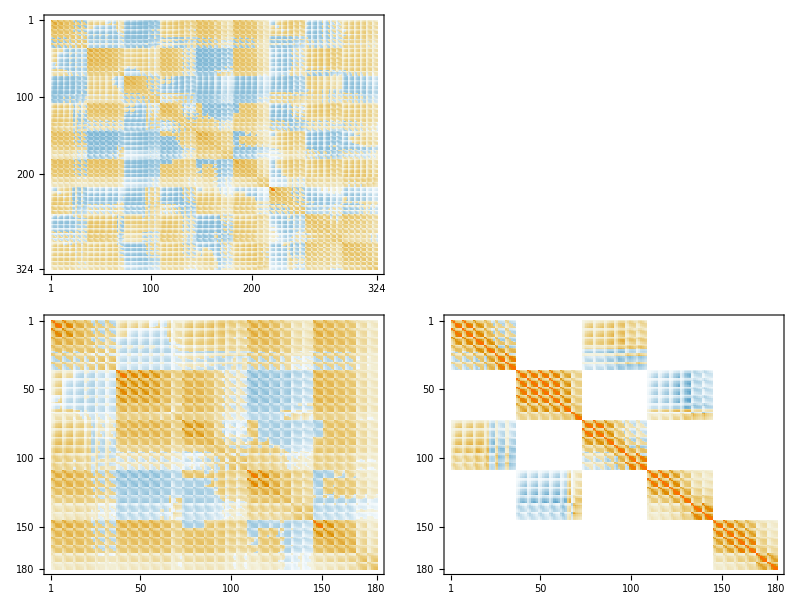

```mathematica
of=0;
DlikeS=Range[1+of,72,1];
DlikeD=Range[109+of,216,1];
DlikeRange=Join[DlikeS,DlikeD];
(*DlikeRange=Range[5,125,1]*)
If[(Length[DlikeRange]!=(Length[DevecGSp] DAdim)),Print["selected number of states ≠ Dim(D⊗a)  ",Length[DlikeRange],"≠",Length[DevecGSp] DAdim]];
DlikePartofH=FSHamBare[[1]][[1]][[DlikeRange,DlikeRange]];
DlikePartofN=FSNormBare[[1]][[1]][[DlikeRange,DlikeRange]];
orderedEVDr=Sort[Transpose[Eigensystem[{DlikePartofH,DlikePartofN}]],Re[#1[[1]]]<Re[#2[[1]]]&];
DevalGSr=orderedEVDr[[1]][[1]];
DevecGSr=orderedEVDr[[1]][[2]];
Print["Vector norm of GS (generalized EVP) = ",Norm[DevecGSr]];
Print["B(in reduced, D-like space) = ",Style[DevalGSr,Red]," MeV"];

DBasisDim=Length[DevecGSr];
Print["Deuteron-basis Dimension = ",DBasisDim];
Grid[{{MatrixPlot[FSHamBare[[1]][[1]],ImageSize->Large],MatrixPlot[FSNormBare[[1]][[1]],ImageSize->Large]},{MatrixPlot[DlikePartofH,ImageSize->Large],MatrixPlot[DlikePartofN,ImageSize->Large]}}]
```

for each of the states with the deuteron quantum numbers on the first two particles, there are a number of other which couple the third particle in appropriate ways *and* each vector’s radial dependence is expanded with a constant number of Gaussians. Hence the larger block size. In the example above, the S-wave cfg comprises two block each of side length 20=5 (particle1,2 widths) · 4(particle3 widths); the two blocks are ⊥ because they couple to a total spin 1/2 and 3/2 while being identical in their coordinate-space coupling structure.
c_1^(s)→1…4, c_2^(s)→5…8, …, c_10^(s)→1…40
c_11^(d)→61…64, c_12^(d)→65…68, …, c_25^(d)→117…120
A specific state Dais parametrized by selecting *one* index per block; a physically-inspired choice is to choose the largest index as that conventionally corresponds to the largest width, i.e., the broadest Gaussian and thereby a relatively large separation between the cm of particles 12 and the 3rd one.

we obtain all the other Da,a∈{1,2,...,4^(dim(D))}, in principle, by distributing the D’s expansion coefficients c_j appropriately in the vector cj; however, since 4^25 is quite a large number, we start with a random subset.

```mathematica
ResourceFunction["NineJSymbol"][({{l1,0.,l1},{1.,1./2.,sS},{1.,1./2.,Subscript[S, c]}})]
nineJSymbol[{l1,0.,l1},{1.,1./2.,sS},{1.,1./2.,Subscript[S, c]}]
```

0.288675

0.288675

```mathematica
ciAs={};
UeCo=DevecGSp;
Subscript[S, c]=1./2.;
jJ=Subscript[I, n][[1]];
Do[
aI={};
bvn=1;
tmp=ConstantArray[0,FSbasisDim[[1]][[1]]];

Do[

Which[
0<bvn<=6,
l1=0;lxi=1;lL=1;sS=1/2;,
7<=bvn<=12,
l1=0;lxi=1;lL=1;sS=3/2;,
19<=bvn<=24,
l1=2;lxi=1;lL=1;sS=1/2;,
25<=bvn<=30,
l1=2;lxi=1;lL=1;sS=3/2;,
31<=bvn<=36,
l1=2;lxi=1;lL=2;sS=3/2;
];

lb=DAdim bv;
(* widths are ordered descending; hence, ub-1 selects a small one in order
"to keep the 3rd particle away from the deuteron" *)
aInd=lb+Na;(*RandomInteger[{lb,ub}];*)

(*coeff=UeCo[[bvn]] √6 (-1)^(lxi+l1+sS+jJ) Hat[l1] Hat[lL]Hat[sS]Hat[Subscript[S, c]] SixJSymbol[{lL,sS,jJ},{Subscript[S, c],lxi,l1}] ResourceFunction["NineJSymbol"][({{l1,0.,l1},{1.,1./2.,sS},{1.,1./2.,Subscript[S, c]}})];*)
coeff=UeCo[[bvn]] √6 (-1)^(lxi+l1+sS+jJ) Hat[l1] Hat[lL]Hat[sS]Hat[Subscript[S, c]] SixJSymbol[{lL,sS,jJ},{Subscript[S, c],lxi,l1}] nineJSymbol[{l1,0.,l1},{1.,1./2.,sS},{1.,1./2.,Subscript[S, c]}];

AppendTo[aI,{aInd,coeff}];
bvn+=1;
,{bv,DbvIndices}];

Do[
tmp[[m[[1]]]]=m[[2]];
,{m,aI}];

AppendTo[ciAs,tmp];
,{Na,DAdim}];

(#//MatrixForm)&/@ciAs
```

{(-0.00347769
0
0
0
0
0
-0.238772
0
0
0
0
0
-0.000692263
0
0
0
0
0
-0.000791676
0
0
0
0
0
-0.00021863
0
0
0
0
0
0.000125863
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
-0.00171106
0
0
0
0
0
0.0269892
0
0
0
0
0
0.0121917
0
0
0
0
0
0.000887309
0
0
0
0
0
-0.000516385
0
0
0
0
0
-0.0000131732
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
-0.00347769
0
0
0
0
0
-0.238772
0
0
0
0
0
-0.000692263
0
0
0
0
0
-0.000791676
0
0
0
0
0
-0.00021863
0
0
0
0
0
0.000125863
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
-0.00171106
0
0
0
0
0
0.0269892
0
0
0
0
0
0.0121917
0
0
0
0
0
0.000887309
0
0
0
0
0
-0.000516385
0
0
0
0
0
-0.0000131732
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
-0.00347769
0
0
0
0
0
-0.238772
0
0
0
0
0
-0.000692263
0
0
0
0
0
-0.000791676
0
0
0
0
0
-0.00021863
0
0
0
0
0
0.000125863
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
-0.00171106
0
0
0
0
0
0.0269892
0
0
0
0
0
0.0121917
0
0
0
0
0
0.000887309
0
0
0
0
0
-0.000516385
0
0
0
0
0
-0.0000131732
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
-0.00347769
0
0
0
0
0
-0.238772
0
0
0
0
0
-0.000692263
0
0
0
0
0
-0.000791676
0
0
0
0
0
-0.00021863
0
0
0
0
0
0.000125863
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
-0.00171106
0
0
0
0
0
0.0269892
0
0
0
0
0
0.0121917
0
0
0
0
0
0.000887309
0
0
0
0
0
-0.000516385
0
0
0
0
0
-0.0000131732
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
-0.00347769
0
0
0
0
0
-0.238772
0
0
0
0
0
-0.000692263
0
0
0
0
0
-0.000791676
0
0
0
0
0
-0.00021863
0
0
0
0
0
0.000125863
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
-0.00171106
0
0
0
0
0
0.0269892
0
0
0
0
0
0.0121917
0
0
0
0
0
0.000887309
0
0
0
0
0
-0.000516385
0
0
0
0
0
-0.0000131732
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
-0.00347769
0
0
0
0
0
-0.238772
0
0
0
0
0
-0.000692263
0
0
0
0
0
-0.000791676
0
0
0
0
0
-0.00021863
0
0
0
0
0
0.000125863
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
0.
0
0
0
0
0
-0.00171106
0
0
0
0
0
0.0269892
0
0
0
0
0
0.0121917
0
0
0
0
0
0.000887309
0
0
0
0
0
-0.000516385
0
0
0
0
0
-0.0000131732
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)}

```mathematica
esysFSp[[Jf]][[Basf]][[1]][[2]].Tik
```

{0.196096,-0.0023932,4.01388×10^-6,-0.0000104889,3.3205×10^-6,-2.14208×10^-6,-0.19538,0.00238647,-3.57868×10^-6,7.13379×10^-6,-1.44653×10^-6,1.50859×10^-6,-0.470253,0.00572309,-0.0000136012,0.0000511793,-0.0000214887,0.0000137814,-0.577859,0.00713347,-0.000024952,0.000188868,-0.0000356531,0.0000124493,-0.0792502,-0.000259181,-0.0000248262,-1.49102×10^-6,-9.14693×10^-6,2.75273×10^-6,0.0317787,0.00603521,0.000077092,-0.0000401611,0.0000257113,-7.73515×10^-6,0.00688908,6.79671×10^-6,8.93456×10^-6,-1.48631×10^-7,6.44947×10^-6,-2.43867×10^-6,-0.405307,-0.000925003,-0.000498485,-0.000263892,-0.000542096,0.00045074,0.408707,0.000937008,0.000501771,0.000271103,0.000549722,-0.00046036,-0.0148522,-0.0000238135,-0.0000176613,-9.39303×10^-6,-0.0000212211,0.0000172374,-0.0182121,0.0000449929,-0.0000206365,-6.38772×10^-6,0.0000118042,-0.0000102093,-0.000583242,-0.000263187,0.0000193888,-0.0000101155,6.0742×10^-6,-1.92068×10^-6,-3.99039×10^-7,-1.35844×10^-6,2.65874×10^-7,-2.78074×10^-6,1.30917×10^-6,6.31839×10^-7,5.68422×10^-7,1.88993×10^-6,-7.77075×10^-7,3.9306×10^-6,-2.5426×10^-6,-8.01183×10^-7,-9.98768×10^-7,-3.59034×10^-6,9.701×10^-7,-0.0000108375,4.26217×10^-6,6.43099×10^-6,9.3319×10^-6,0.0000326072,-6.12898×10^-6,0.000132234,0.0000400801,-0.0000129499,-0.000263548,-0.000897547,0.00030474,-0.000199124,0.0000989425,-0.0000283369,0.000491037,0.00605079,-0.000430439,0.000285392,-0.000146122,0.0000418645,0.00316682,-2.20553×10^-6,3.98669×10^-6,-1.70324×10^-6,4.22166×10^-6,-1.04119×10^-6,-0.000655174,1.21656×10^-6,-9.38733×10^-7,1.40281×10^-6,-3.30793×10^-6,1.53975×10^-6,0.00212001,3.18386×10^-6,3.80559×10^-6,-4.27883×10^-6,8.74358×10^-6,-3.84737×10^-6,0.000683989,2.71255×10^-6,8.19329×10^-6,-0.0000254894,-4.65416×10^-6,-6.32732×10^-7,-0.0000138266,-0.000197718,0.000197663,-0.0000536076,0.0000370719,-0.0000109277,-0.0000158202,0.000381097,-0.00030761,0.000135526,-0.000076377,0.0000228387,0.00608052,-0.0000754318,8.2025×10^-8,-1.05943×10^-6,3.28753×10^-7,-1.45522×10^-7,0.0584428,-0.000724826,-1.08178×10^-7,-2.06404×10^-6,1.79109×10^-7,-7.10542×10^-7,0.0990304,-0.00122893,1.57807×10^-7,-9.30379×10^-6,1.41666×10^-6,-1.14025×10^-6,0.0585957,-0.000725389,-2.02642×10^-6,0.0000230162,0.0000143344,5.64896×10^-6,0.000748874,-0.000282778,0.000044451,-0.0000552194,0.0000302297,-9.64995×10^-6,-0.000372159,0.0022437,0.0000140633,3.9488×10^-6,-2.71753×10^-6,1.07022×10^-6,0.0162033,-0.000194476,7.07436×10^-7,-7.74762×10^-7,4.98005×10^-7,-2.35825×10^-7,0.0710614,-0.00085253,2.9144×10^-6,-5.98623×10^-6,2.65068×10^-6,-8.38046×10^-7,0.0505377,-0.000605896,2.59413×10^-6,-2.47822×10^-7,1.83337×10^-6,-1.45127×10^-6,0.0656684,-0.000788006,1.88441×10^-6,-0.0000101278,1.35604×10^-6,5.43024×10^-7,0.00561767,-0.0000517162,-0.0000267444,0.0000578164,-0.0000288696,8.8451×10^-6,-0.00128459,-0.000580642,-0.0000453866,0.0000202808,-0.0000106057,3.15356×10^-6,1.22626×10^-9,-4.72416×10^-9,-7.12946×10^-9,7.52696×10^-9,1.08934×10^-9,4.66792×10^-9,-2.56325×10^-8,1.00959×10^-7,1.56895×10^-7,1.12427×10^-7,-2.83277×10^-7,3.03526×10^-7,2.46366×10^-7,-9.57464×10^-7,-9.63692×10^-7,-3.72823×10^-7,4.51022×10^-6,-1.92429×10^-6,-2.66469×10^-6,0.0000105772,7.5864×10^-6,-0.0000182911,-0.0000163194,4.97714×10^-6,0.0000704645,-0.000250274,0.000130515,-0.0000383878,0.0000190001,-6.03651×10^-6,-0.000138889,0.0005453,-0.000234349,0.000107732,-0.0000518965,0.0000160037,-1.90338×10^-8,3.95439×10^-8,-1.67238×10^-6,2.65109×10^-6,-2.68272×10^-6,1.21646×10^-6,9.08531×10^-8,-1.70664×10^-7,6.94187×10^-6,-0.0000120581,7.76077×10^-6,-5.32884×10^-6,-7.87579×10^-7,8.84555×10^-7,-0.0000582134,0.0000772615,-0.0000187219,0.0000245008,1.06576×10^-6,-1.91203×10^-8,0.0000679511,-0.0000462961,0.0000326067,-0.00001364,-0.0000104543,-0.0000319437,-0.0000985297,0.000030821,-0.0000122876,2.86648×10^-6,-0.0000213077,0.00182023,2.55506×10^-6,0.0000172827,-0.0000102007,3.67815×10^-6,-1.12589×10^-8,-1.10637×10^-7,1.10295×10^-6,-1.9202×10^-6,1.05933×10^-6,-7.40772×10^-7,2.24769×10^-7,1.41579×10^-6,-0.0000151937,0.0000216546,-9.53317×10^-6,2.67365×10^-6,-4.08768×10^-7,-2.62934×10^-6,0.0000276715,-0.0000402521,0.0000146897,-3.97464×10^-6,7.21081×10^-7,4.26293×10^-6,-0.0000505702,0.0000487202,-6.58633×10^-6,4.45705×10^-6,-5.71144×10^-6,-0.0000379394,0.0000863783,-0.0000119113,1.99192×10^-6,-6.83133×10^-7,0.0000170729,0.000635215,-0.0000454258,0.0000140834,-5.57947×10^-6,1.7185×10^-6}

```mathematica
DaEn[[1]][[1]]
```

0.102684

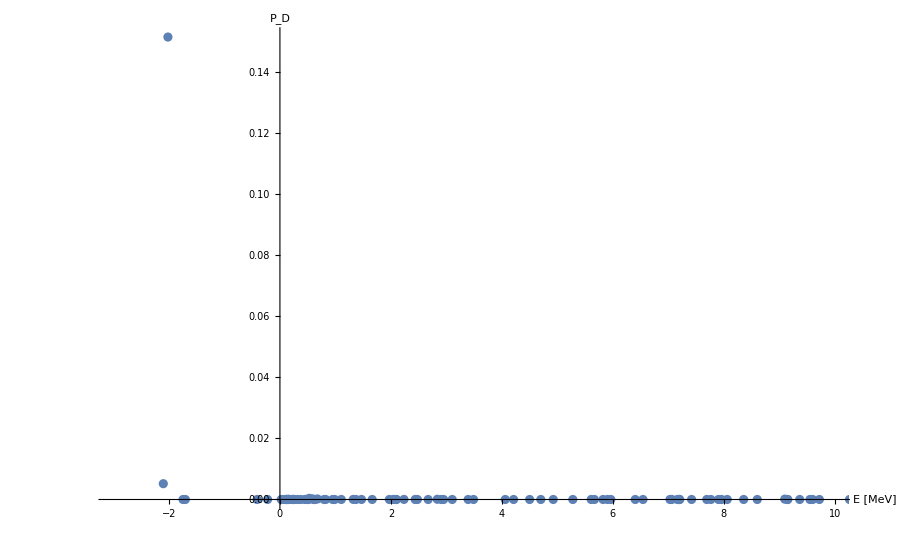

```mathematica
Jf=1;Basf=1;aA=2;bB=aA;
nij=FSNormBare[[Jf]][[Basf]];
nab=Table[ciAs[[a]].nij.ciAs[[b]],{a,DAdim},{b,DAdim}];
Tik=IdentityMatrix[Dimensions[fulltrafosαβInstab[[Jf]][[Basf]]]];(*fulltrafosαβInstab[[Jf]][[Basf]];*)
(*Print["TemplateBox[{\"Da\", \"Db\"},\"BraKet\"] = ",nab//MatrixForm,"     SuperscriptBox[TemplateBox[{\"Da\", \"Db\"},\"BraKet\"], RowBox[{\"-\", \"1\"}]] = ",Inverse[nab]//MatrixForm]*)
DaEn=Table[ciAs[[a]].nij.esysFSp[[Jf]][[Basf]][[eE]][[2]],{eE,FSbasisDim[[Jf]][[Basf]]},{a,DAdim}];
maxEindex=FSbasisDim[[Jf]][[Basf]];
DaNDb=Table[{esysFSp[[Jf]][[Basf]][[EE]][[1]],(DaEn[[EE]][[aA]] Inverse[nab][[aA]][[bB]] DaEn[[EE]][[bB]])},{EE,maxEindex}];
(*DaNDb=Table[{esysFSp[[Jf]][[Basf]][[EE]][[1]],Total[Table[DaEn[[EE]][[a]] Inverse[nab][[a]][[b]] DaEn[[EE]][[b]],{a,DAdim},{b,DAdim}],2]},{EE,maxEindex}];*)
ListPlot[DaNDb,AxesLabel->{"E [MeV]","P_D"},ImageSize->ImgSize,PlotRange->{{-3,10},All}]
```

```mathematica
Jf=1;Basf=1;
nij=FSNormBare[[Jf]][[Basf]];
hij=FSHamBare[[Jf]][[Basf]];
aa=6;bb=6;

hab=ciAs[[aa]].hij.ciAs[[bb]]
nab=ciAs[[aa]].nij.ciAs[[bb]]
hab/nab
```

21.9461

0.0600494

365.468

“sanity” check:  what is ∑_(n=0)^(FS-dim) P_D(E^(n))=?
this is a treacherous sum as it brings us back to what reality P_D  is connected with.

```mathematica
Total[DaNDb[[All,2]]]
```

0.0356643

#### Read RHS ⟨α|O_Lm_L|n⟩

the calculation is parallel in n_k parts

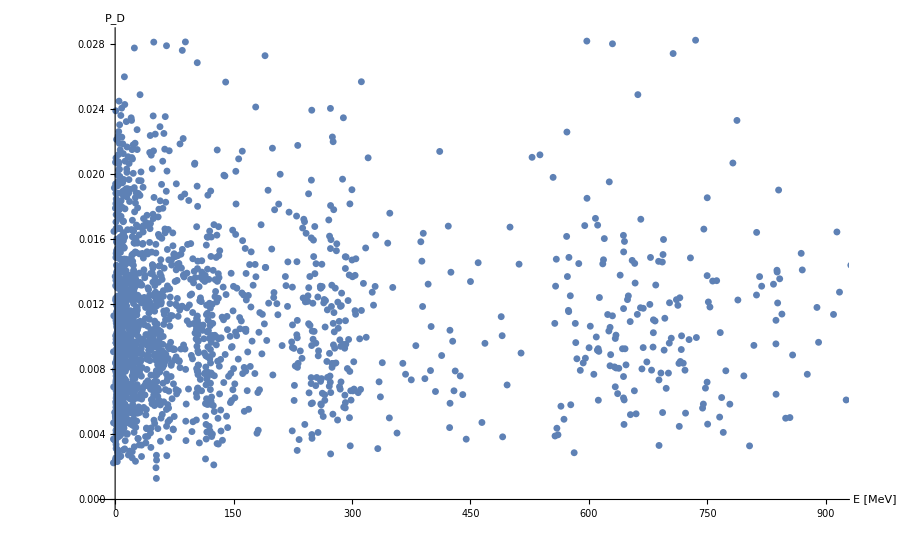
```mathematica
Show[-Graphics-,PlotRange->{{-3,5},Automatic}]
```